# WCG analysis diff 1946-1970

## Directory

```mathematica
datadir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

## Program

```mathematica
largestPosition[l_List]:=Module[{largest},
largest=Max[l];
Position[l,largest]
]
```

```mathematica
selectEdgeAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association];*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]
]
```

```mathematica
selectGraphAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association];*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectGraphAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association]*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectEdgeAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association]*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]
]
```

## Basic information

上位1%被引用論文 {citingPMID(代表) -> citedPMID, count}

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1perc-cited-artByyear.save"];
```

```mathematica
Do[citedPMIDTop1perc[n]=Map[#[[1,2]]&,citedArtlistTop1perc[n]],
{n,1950,2020,5}]
```

## Previous : WCG 1946 - 1965

### Data

```mathematica
previousG=1965
```

1965

Graph

```mathematica
file[previousG]=datadir<>"WCG_1946-"<>ToString[previousG]<>".wl"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/WCG_1946-1965.wl

前世代WCG数*

```mathematica
(WCGlist[previousG]=Get[file[previousG]])//Length
```

5729

WCGをVertexListにする：

```mathematica
(WCGlistV[previousG]=Map[VertexList,WCGlist[previousG]])//Length
```

5729

Vertex名(PMID)からそのVertexがどのWCGに含まれるかそのpositionを返す。

```mathematica
PMIDtoWCGPos[previousG]=Association[Flatten[MapIndexed[Apply[Outer,{Rule,#1,#2}]&,WCGlistV[previousG]]]];
```

```mathematica
largestWCGPos[previousG]=Flatten[largestPosition[Map[VertexCount,WCGlist[previousG]]]]
```

{1}

```mathematica
WCGlargest[previousG]=WCGlist[previousG][[1]];
```

Nodes

```mathematica
(WCGNodes[previousG]=Map[VertexList,WCGlist[previousG]])//Length
```

5729

Edges

```mathematica
(WCGEdges[previousG]=Map[EdgeList,WCGlist[previousG]])//Length
```

5729

Global Graph

```mathematica
GlobalGraph[previousG]=Graph[Flatten[WCGEdges[previousG]]];
```

## Current : WCG 1946 - 1970

### Data

```mathematica
currentG=1970
```

1970

Graph

```mathematica
file[currentG]=datadir<>"WCG_1946-"<>ToString[currentG]<>".wl"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/WCG_1946-1970.wl

```mathematica
(WCGlist[currentG]=Get[file[currentG]])//Length
```

7020

WCGをVertexListにする：

```mathematica
(WCGlistV[currentG]=Map[VertexList,WCGlist[currentG]])//Length
```

7020

Vertex名(PMID)からそのVertexがどのWCGに含まれるかそのpositionを返す。

```mathematica
PMIDtoWCGPos[currentG]=Association[Flatten[MapIndexed[Apply[Outer,{Rule,#1,#2}]&,WCGlistV[currentG]]]];
```

```mathematica
largestWCGPos[currentG]=Flatten[largestPosition[Map[VertexCount,WCGlist[currentG]]]]
```

{1}

```mathematica
WCGlargest[currentG]=WCGlist[currentG][[1]];
```

Nodes

```mathematica
(WCGNodes[currentG]=Map[VertexList,WCGlist[currentG]])//Length
```

7020

Edges

```mathematica
(WCGEdges[currentG]=Map[EdgeList,WCGlist[currentG]])//Length
```

7020

Global Graph

```mathematica
GlobalGraph[currentG]=Graph[Flatten[WCGEdges[currentG]]];
```

```mathematica
(*GlobalEdge[currentG]=EdgeList[GlobalGraph[currentG]];*)
```

## Diff : 1946-1965 < 1946-1970

A. 新規に発生した引用*

```mathematica
(WCGtotaledgeDiff[previousG,currentG]=Complement[Flatten[Map[EdgeList,WCGlist[currentG]]],Flatten[Map[EdgeList,WCGlist[previousG]]]])//Length
```

818629

B. 新規に発生した引用関係からSrc/Dstを混ぜてVertexListをつくる

```mathematica
(WCGtotalnodeDiffU[previousG,currentG]=Union[Flatten[Apply[List,WCGtotaledgeDiff[previousG,currentG],Infinity]]])//Length
```

379982

B-1. 上記VertexListより前年代のVertexでもあるものを選択（グラフを拡張するキーとなる存在:コネクション論文）

```mathematica
(WCGtotalnodeIS[previousG,currentG]=Intersection[Flatten[WCGNodes[previousG]],WCGtotalnodeDiffU[previousG,currentG]])//Length
```

131813

B-2. 上記Vertexに含まれるtop1%論文（コネクション論文かつtop1%論文）-> citedPMIDTop1percCon

```mathematica
citedPMIDTop1percCon[previousG]=Intersection[citedPMIDTop1perc[previousG],WCGtotalnodeIS[previousG,currentG]]
```

{12989928,12991237,13130792,13249955,13262900,13276348,13286333,13293190,13319380,13428781,13475399,13563554,13610936,13718526,13764136,13975866,13986422,14381428,14381429,14454024,14775715,14794694,14803635,14822727,14848424,14898516,14907661,14907713,14915960,14927572,14927794,14938350,15395569,15398090,15404816,15421999,15436457,16695228,16745305,16746620,16747230,16747508,16747652,16747784,16747948,16748273,16748381,16991506,17247100,18128147}

B-3. 新規に発生した引用のうち主要論文に対する引用*

:まずAssociationを作成:

```mathematica
WCGtotaledgeDiffGatherDSTAs=Association[Map[#[[1,2]]->#&,GatherBy[WCGtotaledgeDiff[previousG,currentG],#[[2]]&]]];
```

:AssociationをMap:

```mathematica
(fconEdgediff[currentG]=Map[WCGtotaledgeDiffGatherDSTAs,citedPMIDTop1percCon[previousG]]//Flatten)//Length
```

9219

## WCG connection of all of previous part

A-1. 新規に発生した引用関係により結合が発生した前世代WCG {WCG ID, count} (すべてが結合されたわけではない)

```mathematica
newConnectedWCGcount[currentG]=(previousWCGfconPartAll[currentG]=Cases[Map[PMIDtoWCGPos[previousG],WCGtotalnodeIS[previousG,currentG]],_Integer]//Tally)//Length
```

1411

## WCG elongation matrix : 1946-1965 < 1946-1970

Current WCGのPMIDより、{previous-WCG-ID : current-WCG-ID}のペアを作成する。
Current WCGのPMID（デスティネーション）を渡すと前世代WCGのID（位置）を返す関数を作成する。

```mathematica
aspv=Association[Flatten[Table[Map[#->n&,VertexList[WCGlist[previousG][[n]]]],{n,Length[WCGlist[previousG]]}]]];
```

```mathematica
(cedList=Map[Map[#[[2]]&,EdgeList[#]]&,WCGlist[currentG]])//Length
```

7020

```mathematica
Timing[(elMat[currentG]=DeleteCases[Map[Map[aspv[#]&,#]&,cedList],_Missing,{2}])//Length]
```

{1.2188,7020}

```mathematica
Save[datadir<>"elongationMat.save",elMat]
```

## WCG elongation connection : 1946-1965 < 1946-1970

A-2. 新規に発生した引用関係に対して前世代の引用先がどのWCGに属するか(Missingあり <- 落としている) {“PMID” -> WCG ID}

```mathematica
(WCGtotaledgeDiffEff[previousG,currentG,"previous WCG ID"]=Cases[  Map[#[[1]]->PMIDtoWCGPos[previousG][#[[2]]]&,WCGtotaledgeDiff[previousG,currentG]]  ,x_/;Head[x[[2]]]==Integer])//Length
```

401592

ギャザー.ユニーク化

```mathematica
(WCGconUnion[previousG,currentG,"previous WCG ID"]=Map[Union,  GatherBy[WCGtotaledgeDiffEff[previousG,currentG,"previous WCG ID"],#[[1]]&]  ])//Length
```

60660

A-3. 新規に発生した引用関係により異なる前世代WCGを結合する論文（ユニーク化）

```mathematica
newMetaconnectedcount[currentG]=(WCGelongationconUnion[previousG,currentG,"previous WCG ID"]=Cases[WCGconUnion[previousG,currentG,"previous WCG ID"],x_/;Length[x]>1])//Length
```

1937

A-4. 新規に結合された前世代WCG（全てが統合された訳ではない）

```mathematica
newMetaconnectedWCGcount[currentG]=(WCGnewconnected[previousG,currentG]=Union[Map[#[[2]]&,Flatten[WCGelongationconUnion[previousG,currentG,"previous WCG ID"]]]])//Length
```

1133

## Visualization (top 1% article part)

### グラフの主要接続部分のパターン定義

主要接続部分とはグラフ差分のうちで主要論文が関与する部分。本研究の流れではフォワードコネクション （主要論文の被引用） を使うのが妥当か。

コネクション論文かつ上位1%論文付近のネットワーク（当年代）

:フォワードコネクション（上位1%コネクション論文が引用される;年代を進める）-> citedPMIDTop1percCon[previousG]

### 1970におけるグラフの接続部分

#### *フォワード

関数のSubgraph[]と同じ結果が欲しければ、結果のvertexlistをキーにしてSubgraph[]する。（今回不要なはず）

```mathematica
fconGraph[currentG]=selectGraphAs["DST"][GlobalGraph[currentG],citedPMIDTop1percCon[previousG]];
```

```mathematica
vl=VertexList[fconGraph[currentG]];
```

```mathematica
(fconEdgelist[currentG]=EdgeList[fconGraph[currentG]])//Length
```

18457

```mathematica
(fconNodelist[currentG]=VertexList[fconGraph[currentG]])//Length
```

13995

#### *バックワード

```mathematica
(fconEdgeSRC[currentG]=Union[Map[#[[1]]&,fconEdgelist[currentG]]])//Length
```

13959

```mathematica
AbsoluteTiming[bconGraph[currentG]=selectGraphAs["SRC"][GlobalGraph[currentG],fconEdgeSRC[currentG]]]
```

{2.47712,}

```mathematica
(bconNodelist[currentG]=VertexList[bconGraph[currentG]])//Length
```

103933

top1%論文による前世代グラフのWCG接続

```mathematica
previousWCGfconPartTop1perc[currentG]=Cases[Map[PMIDtoWCGPos[previousG],bconNodelist[currentG]],_Integer]//Tally//Sort
```

{{1,64224},{122,1},{199,3},{210,1},{245,1},{283,1},{338,3},{369,1},{508,2},{525,1},{541,1},{617,1},{677,1},{685,1},{782,2},{837,1},{856,1},{1001,1},{1056,3},{1071,1},{1088,1},{1089,1},{1094,1},{1101,1},{1148,1},{1180,1},{1226,1},{1300,1},{1365,1},{1727,1},{1936,1},{1982,1},{2066,1},{2116,1},{2136,1},{2182,1},{2217,1},{2219,1},{2260,3},{2310,1},{2548,2},{2801,1},{2948,1},{2952,1},{2973,1},{3069,1},{3237,1},{3308,1},{3684,1},{3714,1},{3889,1},{4035,1},{4036,1},{4078,1},{4164,1},{4305,2},{4345,2},{4550,1},{4615,1},{4623,1},{4648,1},{4681,1},{4707,1},{4805,2},{4911,1},{5216,1},{5391,1},{5564,1}}

```mathematica
(*Export["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/connectionpartGraph_"<>ToString[previousG]<>"-"<>ToString[currentG]<>".wl",bconGraph[currentG]]*)
```

### 上位1%論文による1965と1970のグラフの差分

#### *フォワード : 差分

```mathematica
vstyle=Map[#->Orange&,citedPMIDTop1percCon[previousG]]
```

{12989928→RGBColor[1, 0.5, 0],12991237→RGBColor[1, 0.5, 0],13130792→RGBColor[1, 0.5, 0],13249955→RGBColor[1, 0.5, 0],13262900→RGBColor[1, 0.5, 0],13276348→RGBColor[1, 0.5, 0],13286333→RGBColor[1, 0.5, 0],13293190→RGBColor[1, 0.5, 0],13319380→RGBColor[1, 0.5, 0],13428781→RGBColor[1, 0.5, 0],13475399→RGBColor[1, 0.5, 0],13563554→RGBColor[1, 0.5, 0],13610936→RGBColor[1, 0.5, 0],13718526→RGBColor[1, 0.5, 0],13764136→RGBColor[1, 0.5, 0],13975866→RGBColor[1, 0.5, 0],13986422→RGBColor[1, 0.5, 0],14381428→RGBColor[1, 0.5, 0],14381429→RGBColor[1, 0.5, 0],14454024→RGBColor[1, 0.5, 0],14775715→RGBColor[1, 0.5, 0],14794694→RGBColor[1, 0.5, 0],14803635→RGBColor[1, 0.5, 0],14822727→RGBColor[1, 0.5, 0],14848424→RGBColor[1, 0.5, 0],14898516→RGBColor[1, 0.5, 0],14907661→RGBColor[1, 0.5, 0],14907713→RGBColor[1, 0.5, 0],14915960→RGBColor[1, 0.5, 0],14927572→RGBColor[1, 0.5, 0],14927794→RGBColor[1, 0.5, 0],14938350→RGBColor[1, 0.5, 0],15395569→RGBColor[1, 0.5, 0],15398090→RGBColor[1, 0.5, 0],15404816→RGBColor[1, 0.5, 0],15421999→RGBColor[1, 0.5, 0],15436457→RGBColor[1, 0.5, 0],16695228→RGBColor[1, 0.5, 0],16745305→RGBColor[1, 0.5, 0],16746620→RGBColor[1, 0.5, 0],16747230→RGBColor[1, 0.5, 0],16747508→RGBColor[1, 0.5, 0],16747652→RGBColor[1, 0.5, 0],16747784→RGBColor[1, 0.5, 0],16747948→RGBColor[1, 0.5, 0],16748273→RGBColor[1, 0.5, 0],16748381→RGBColor[1, 0.5, 0],16991506→RGBColor[1, 0.5, 0],17247100→RGBColor[1, 0.5, 0],18128147→RGBColor[1, 0.5, 0]}

```mathematica
vsize=Map[#->16&,citedPMIDTop1percCon[previousG]]
```

{12989928→16,12991237→16,13130792→16,13249955→16,13262900→16,13276348→16,13286333→16,13293190→16,13319380→16,13428781→16,13475399→16,13563554→16,13610936→16,13718526→16,13764136→16,13975866→16,13986422→16,14381428→16,14381429→16,14454024→16,14775715→16,14794694→16,14803635→16,14822727→16,14848424→16,14898516→16,14907661→16,14907713→16,14915960→16,14927572→16,14927794→16,14938350→16,15395569→16,15398090→16,15404816→16,15421999→16,15436457→16,16695228→16,16745305→16,16746620→16,16747230→16,16747508→16,16747652→16,16747784→16,16747948→16,16748273→16,16748381→16,16991506→16,17247100→16,18128147→16}

新しく増えた引用関係（currentのconエッジ - previousのconエッジ）のハイライト

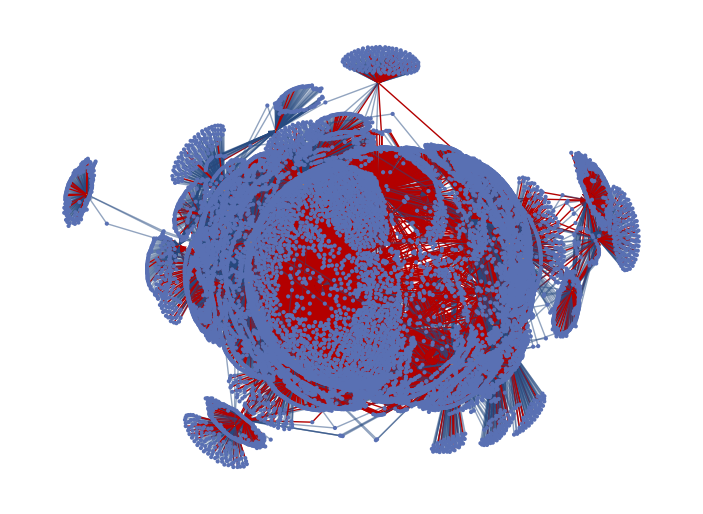

```mathematica
fconGraphD[currentG]=Graph[fconGraph[currentG],GraphHighlight->Flatten[{fconEdgediff[currentG]}],VertexStyle->vstyle,VertexSize->vsize]
```

可視化対象の構造だけはExportしておく。

```mathematica
(*Export[datadir<>"gdiffF_"<>ToString[currentG]<>".wl",fconGraphD[currentG]]*)
```